# Graph Colorings

Peter Burbery

Abstract

## Vertex Colorings

To color the vertices of a graph, no adjacent vertices can be the same color.

Make the function ColorGraphVertices a persistent function:

```mathematica
ResourceFunction["PersistResourceFunction"][{"PersistResourceFunction","ColorGraphVertices"}];
```

Color the vertices of the Petersen graph:

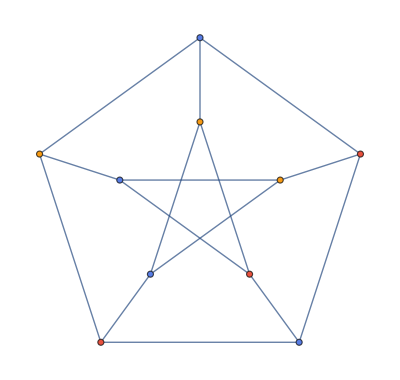

```mathematica
ColorGraphVertices[PetersenGraph[]]
```

Color the vertices of a random graph:

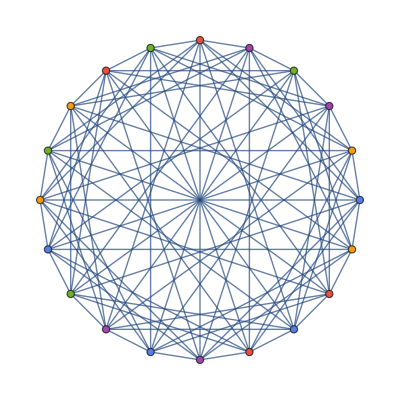

```mathematica
ColorGraphVertices[GraphData@@RandomSample[GraphData[],1]]
```

Make a gallery of graphs with colorings:

```mathematica
ColorGraphVertices/@(GraphData/@RandomSample[GraphData[],10])
```